```mathematica
ClearAll["Global`*"]
```

```mathematica
xmin=1;
xmax=3;
```

```mathematica
(*test case 1*)
```

```mathematica
(*u[x_]:=1+x^2 
Lu[x_]:=2
gradu[x_]:={2 x}*)
```

```mathematica
(*test case 2*)
```

```mathematica
u[x_]:=1+Cos[2π x]/(1+x^2)
Lu[x_]:=(-2 (1-3 x^2+2 π^2 (1+x^2)^2) Cos[2 π x]+8 π x (1+x^2) Sin[2 π x])/((1+x^2)^3)
gradu[x_]:={-(2 (x Cos[2 π x]+π (1+x^2) Sin[2 π x]))/((1+x^2)^2)}
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u_v/solution/nodal_values/u.csv"]
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

4.6875×10^-7

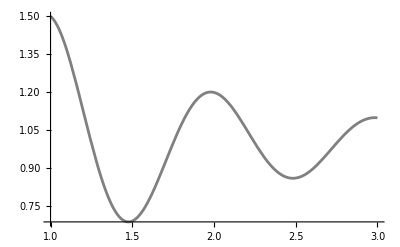

```mathematica
plotexact=Plot[u[x],{x,xmin,xmax},PlotRange->Full,PlotStyle->Gray]
```

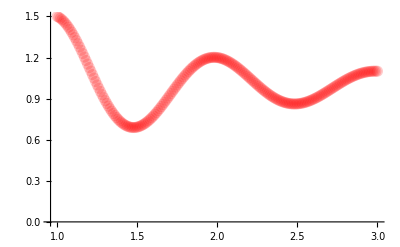

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}]
```

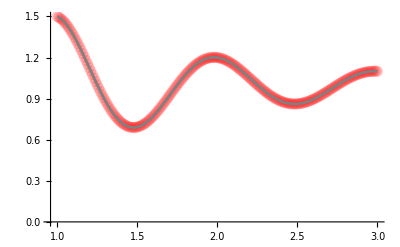

```mathematica
Show[plotnum,plotexact]
```

```mathematica
(*checlk for v*)
```

```mathematica
(*check for v[[1]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u_v/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-gradu[t[[i,1]]][[1]]],{i,1,Length[t]}]]
```

8.0523×10^-7

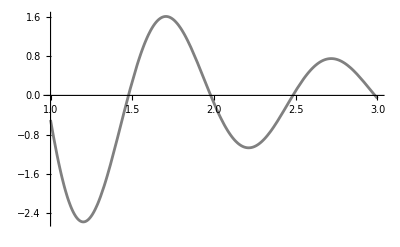

```mathematica
plotexact=Plot[gradu[x][[1]],{x,xmin,xmax},PlotRange->Full,PlotStyle->Gray]
```

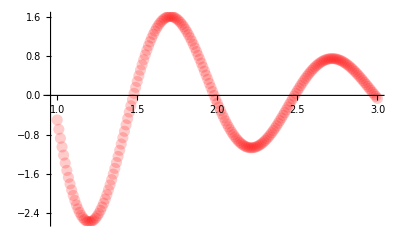

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}]
```

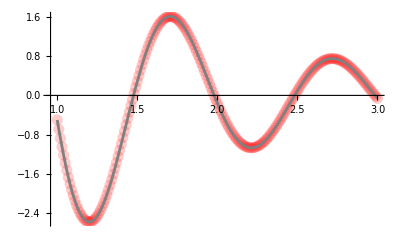

```mathematica
Show[plotnum,plotexact]
```